```mathematica
ClearAll["Global`*"]
NotebookSave[]
```

Initial Parameters

```mathematica
n=50; (*Number of exercise points per year*)
T=2; (*Number of years in the contract*)
R=0.06;(*Year discount factor*)
r=R/n; (*R/nDiscount factor per unit time*)
sigma=0.2; (*Volatility of the option*)
S0=44.; (*Initial price of the option*)
M=1000; (*Number of simulated paths*)
callput="Put"; (*option type: "Put" or "Call"*)
K=40.; (*Strike Price*)
(*S={{1.,1.09,1.08,1.34},{1.,1.16,1.26,1.54},{1.,1.22,1.07,1.03},{1.,0.93,0.97,0.92},{1.,1.11,1.56,1.52},{1.,.76,.77,.90},{1.,.92,.84,1.01},{1.,.88,1.22,1.34}};
n=1; (*Number of exercise points per year*)
T=3; (*Number of years in the contract*)
R=0.06;(*Year discount factor*)
r=R/n; (*Discount factor per unit time*)
S0=1.; (*Initial price of the option*)
M=8; (*Number of simulated paths*)
callput="Put"; (*option type: "Put" or "Call"*)
K=1.1; (*Strike Price*)
regr[x_]=Fit[reg,{1,x,x^2},x];*)
```

```mathematica
a=0.5;b=0.4;w=0.02;
```

Path Simulation

```mathematica
dT=1/n; (*Time step duration*)
S=Table[0,M,n*T+1]; (*Table with all the simulated paths. All entries are initially assigned 0*)
S[[All,1]]=S0; (*Set all paths' starting points to the initial asset price*)
dW=Sqrt[dT]*RandomVariate[NormalDistribution[],{M,n*T}];
sig=Table[sigma,1,M][[1]];
For[i=1,i<=n*T,i++,S[[All,i+1]]=S[[All,i]]+R*dT*S[[All,i]]+sig*S[[All,i]]*dW[[All,i]];sig=Sqrt[a*((S[[All,i+1]]-S[[All,i]])/S[[All,i]])^2+sig^2*b+w]] (*Simulate geometric Brownian Motion: dS=r*S*dt+σ*S*dW *)
```

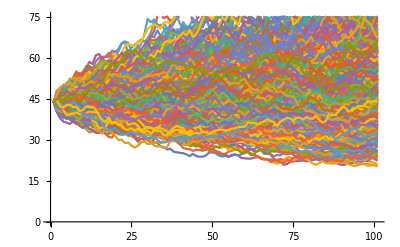

```mathematica
ListPlot[S,Joined->True]
```

Longstaff-Schwartz Method

```mathematica
Payoff[stock_]:=If[callput=="Put",Max[K-stock,0],Max[stock-K,0]]; (*Return Put/Call stike price payoff functions*)
```

```mathematica
cfdisc=Table[0,M,n*T]; (*Matrix with all discounted cash flows*)
cfdisc[[All,n*T]]=Map[Payoff,S[[All,n*T+1]]]*Exp[-R*T]; (*Calculate discounted cash flows at the maturity*)
```

```mathematica
euro=Total[cfdisc,2]/M  (*European option price*);
```

```mathematica
cfreal=Table[0,M,n*T];(*Matrix with all [not-discounted] cash flows*)
cfreal[[All,n*T]]=Map[Payoff,S[[All,n*T+1]]];(*Calculate cash flows at the maturity*)
```

```mathematica
sr=Table[0,M,n*T]; (*Matrix with all recommended exercice decisions. Entry 1 if exercise is recommended at the respective period and 0 otherwise*)
sr[[All,n*T]]=Map[Sign,cfdisc[[All,n*T]]]; (*Obtain all recommended exercise decisions at the maturity*)
```

```mathematica
lastsr[path_]:=FirstPosition[cfdisc[[path]],_?(#≠0&),{0}][[1]] ;(*Auxiliary function to find the recommended exercise time for a given path*)
```

```mathematica
discpayoff[path_,current_]:=If[lastsr[path]≠0,cfreal[[path,lastsr[path]]]*Exp[-r*(lastsr[path]-current)],0];(*Auxiliary function that returns the discounted cash flow between the last recommended exercise time and the "current time", that we are trying to check if is optimal*)
```

```mathematica
Do[
reg={}; (*Matrix with all the current optimal exercise that will be used to fit the Laguerre polynomials*)
Do[If[Payoff[S[[i,j+1]]]>0,AppendTo[reg,{S[[i,j+1]],discpayoff[i,j]}],],{i,1,M}];(*Find where if it is optimal to exercise at the current time and if so, insert a row in the previous matrix*)
regr[x_]=Fit[reg,Exp[-x/2]*{Exp[x/2],LaguerreL[0,x],LaguerreL[1,x],LaguerreL[2,x],LaguerreL[3,x]},x];(*Fit the optimal data*)
Do[If[Payoff[S[[i,j+1]]]>0,If[Payoff[S[[i,j+1]]]>=regr[S[[i,j+1]]], (*if it is recommended to exercise at the current time, update the cash flow tables. otherwise, do nothing*)
cfdisc[[i,All]]=0;
cfreal[[i,All]]=0;
sr[[i,All]]=0;
cfdisc[[i,j]]=Payoff[S[[i,j+1]]]*Exp[-r*j];
cfreal[[i,j]]=Payoff[S[[i,j+1]]];sr[[i,j]]=1,],],{i,1,M}],{j,n*T-1,1,-1}];
```

Final Result

```mathematica
Total[MapIndexed[#1*Exp[-r*First[#2]]&,Transpose[cfreal]],2]/M
```

1.59625

```mathematica
euro (*European option price*)
```

1.31199

```mathematica
Beep[]
```

```mathematica
NotebookSave[]
```